```mathematica
Clear["Global`*"]
```

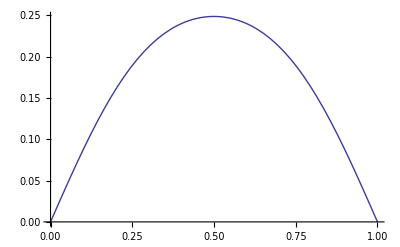
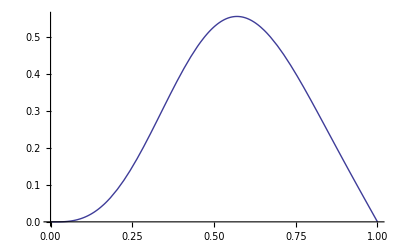
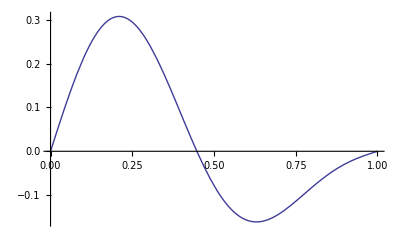
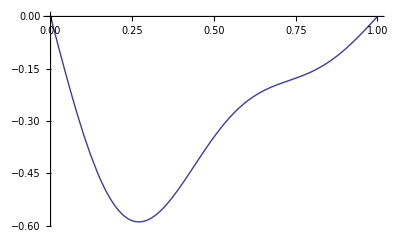
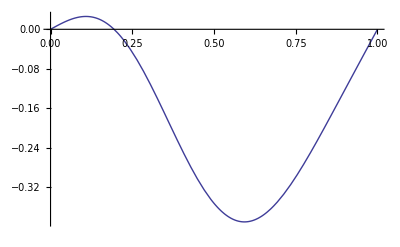
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
u0[x_]:=x (1-x);
u1[x_]:=x^3;
a[n_,l_]:=(2/l) Integrate[u0[x]Sin[(n Pi x) / l],{x,0,l}];
b[n_,l_]:=(2/l) Integrate[u1[x]Sin[(n Pi x) / l],{x,0,l}];
u[N_,x_,t_,l_,c_]:=Sum[ Sin[n Pi x /l](a[n,l] Cos[n Pi c t / l]  + (l / (n Pi c))b[n,l] Sin[(n Pi c t) / l] ),{n,1,N}];
graphu[N_,t_,l_,k_]:= Plot[Evaluate[u[N,x,t,l,k]],{x,0,1}];
Table[graphu[3,t,1.0,.2],{t,0,20,2}]
```